重新排列列表

对于从一个计算中得到的列表，在进入另一个计算之前进行重新排列是很常见的。例如，我们可能有一个包含成对数字的列表，需要把它转换成一对列表，或者反之亦然。

对一个包含成对数字的列表进行转置，使其成为一对列表：

```mathematica
Transpose[{{1,2},{3,4},{5,6},{7,8},{9,10}}]
```

{{1,3,5,7,9},{2,4,6,8,10}}

将这对列表转换回包含成对数字的列表：

```mathematica
Transpose[{{1,3,5,7,9},{2,4,6,8,10}}]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

Thread 是一个密切相关的操作，通常对生成 Graph 的输入有用。

“Thread” → 逐项作用于两个列表的元素：

```mathematica
Thread[{1,3,5,7,9}->{2,4,6,8,10}]
```

{1→2,3→4,5→6,7→8,9→10}

Partition 将一个列表分割成指定大小的块。

将一个包含 12 个元素的列表分割成大小为 3 的块：

```mathematica
Partition[Range[12],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

对一个字符列表进行分割，将其显示在一个网格中：

```mathematica
Grid[Partition[Characters["An array of text made in the Wolfram Language"],9],Frame->All]
```

A | n |   | a | r | r | a | y |  
o | f |   | t | e | x | t |   | m
a | d | e |   | i | n |   | t | h
e |   | W | o | l | f | r | a | m
  | L | a | n | g | u | a | g | e

如果你不指定其它参数，Partition 会把一个列表分割为不重叠的块。但你也可以把列表分割为具有某些指定偏移的块。

将一个列表分割成大小为 3 的块，偏移量为 1：

```mathematica
Partition[Range[10],3,1]
```

{{1,2,3},{2,3,4},{3,4,5},{4,5,6},{5,6,7},{6,7,8},{7,8,9},{8,9,10}}

将一个字符列表分割成偏移量为 1 的块：

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,1],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
o | l | f | r | a | m |   | L | a | n | g | u
l | f | r | a | m |   | L | a | n | g | u | a
f | r | a | m |   | L | a | n | g | u | a | g
r | a | m |   | L | a | n | g | u | a | g | e

使用偏移量 2：

```mathematica
Grid[Partition[Characters["Wolfram Language"],12,2],Frame->All]
```

W | o | l | f | r | a | m |   | L | a | n | g
l | f | r | a | m |   | L | a | n | g | u | a
r | a | m |   | L | a | n | g | u | a | g | e

Partition 是将列表分解为子列表。而 Flatten 则是“压平”子列表。

创建连续整数的各位数的列表的列表：

```mathematica
IntegerDigits/@Range[20]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,0}}

创建一个压平的版本：

```mathematica
Flatten[IntegerDigits/@Range[20]]
```

{1,2,3,4,5,6,7,8,9,1,0,1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,2,0}

根据数字的顺序绘制一个线条图：

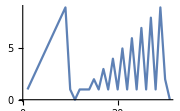

```mathematica
ListLinePlot[Flatten[IntegerDigits/@Range[20]]]
```

Flatten 通常会把所有级别的列表都压平。但很多时候，你只想压平一层列表。这样就创建了一个 4×4 的表，其中每个元素本身就是一个列表。

创建一个列表的列表的列表：

```mathematica
Table[IntegerDigits[i^j],{i,4},{j,4}]
```

{{{1},{1},{1},{1}},{{2},{4},{8},{1,6}},{{3},{9},{2,7},{8,1}},{{4},{1,6},{6,4},{2,5,6}}}

将所有对象都压平：

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}]]
```

{1,1,1,1,2,4,8,1,6,3,9,2,7,8,1,4,1,6,6,4,2,5,6}

只压平一层列表：

```mathematica
Flatten[Table[IntegerDigits[i^j],{i,4},{j,4}],1]
```

{{1},{1},{1},{1},{2},{4},{8},{1,6},{3},{9},{2,7},{8,1},{4},{1,6},{6,4},{2,5,6}}

ArrayFlatten 是 Flatten 的一般形式，以数组的数组为输入，并将它们压平为单独的数组。

这将生成一个深度嵌套的结构，很难理解：

```mathematica
NestList[{{#,0},{#,#}}&,{{1}},2]
```

{{{1}},{{{{1}},0},{{{1}},{{1}}}},{{{{{{1}},0},{{{1}},{{1}}}},0},{{{{{1}},0},{{{1}},{{1}}}},{{{{1}},0},{{{1}},{{1}}}}}}}

ArrayFlatten 能使结构更容易理解一些：

```mathematica
NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
```

{{{1}},{{1,0},{1,1}},{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}}}

使用 ArrayPlot，就能很容易看清发生了什么：

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

生成具有 8 层嵌套的分形谢尔宾斯基图样：

```mathematica
ArrayPlot[Nest[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},8]]
```

-Graphics-

还有许多其他方法来重新排列列表。例如，Split 将把一个列表分割成由相同元素构成的子列表。

将一个列表分割成连续的相同元素的序列：

```mathematica
Split[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1},{2,2},{1,1},{3},{1,1,1},{2}}

另一方面，Gather 将把相同的元素收集在一起，无论它们出现在哪里。

将列表中的相同元素收集在一起：

```mathematica
Gather[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1,1,1,1,1,1},{2,2,2},{3}}

GatherBy 根据对元素应用一个函数的结果来收集这些元素。这个例子里使用了 LetterQ，所以它分别收集了字母和非字母。

根据是否是字母来收集字符：

```mathematica
GatherBy[Characters["It's true that 2+2 is equal to 4!"],LetterQ]
```

{{I,t,s,t,r,u,e,t,h,a,t,i,s,e,q,u,a,l,t,o},{', , , ,2,+,2, , , , ,4,!}}

SortBy 将根据应用一个函数的结果进行排序。

Sort 通常将较短的列表放在较长的列表之前：

```mathematica
Sort[Table[IntegerDigits[2^n],{n,10}]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4}}

这里的 SortBy 被告知按每个列表中的第一个元素排序：

```mathematica
SortBy[Table[IntegerDigits[2^n],{n,10}],First]
```

{{1,6},{1,2,8},{1,0,2,4},{2},{2,5,6},{3,2},{4},{5,1,2},{6,4},{8}}

Sort 将一个列表按顺序排序。Union 还会删除所有重复的元素。

找到所有出现的不同元素：

```mathematica
Union[{1,9,5,3,1,4,3,1,3,3,5,3,9}]
```

{1,3,4,5,9}

你可以使用 Union 来查找出现在几个列表中的任何元素的“并集”。

获得一个出现在任何列表中的所有元素的列表：

```mathematica
Union[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8,5}]
```

{1,2,3,4,5,7,8,9}

找出所有列表中的共同元素：

```mathematica
Intersection[{2,1,3,7,9},{4,5,1,2,3,3},{3,1,2,8}]
```

{1,2,3}

找出哪些元素出现在第一个列表但不在第二个列表中：

```mathematica
Complement[{4,5,1,2,3,3},{3,1,2,8}]
```

{4,5}

寻找出现在英语、瑞典语和土耳其语任意一种语言中的字母：

```mathematica
Union[Alphabet["English"],Alphabet["Swedish"],Alphabet["Turkish"]]
```

{ğ,ş,a,å,ä,b,c,ç,d,e,f,g,h,i,ı,j,k,l,m,n,o,ö,p,q,r,s,t,u,ü,v,w,x,y,z}

出现在瑞典语中，但英语中没有的字母：

```mathematica
Complement[Alphabet["Swedish"],Alphabet["English"]]
```

{å,ä,ö}

你可以应用于列表的另一个函数是 Riffle，它在列表的连续元素之间插入对象：

在一个列表的元素之间插入 x：

```mathematica
Riffle[{1,2,3,4,5},x]
```

{1,x,2,x,3,x,4,x,5}

在字符列表中插入 --：

```mathematica
Riffle[Characters["WOLFRAM"],"--"]
```

{W,--,O,--,L,--,F,--,R,--,A,--,M}

将所有对象连接在一起，形成一个单一的字符串：

```mathematica
StringJoin[Riffle[Characters["WOLFRAM"],"--"]]
```

W--O--L--F--R--A--M

像 Partition 这样的函数可以让你把一个列表分解成子列表。有时你只想从一个可能的元素集合开始，然后从这些元素创建列表。

Permutations 将给出一个列表的所有可能的排序，或者说排列组合。

生成 3 个元素一共 3!=3×2×1=6 种可能的排列组合的列表：

```mathematica
Permutations[{Red,Green,Blue}]
```

{{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0]}}

生成 3 个元素一共 2^3=8 个可能的子集：

```mathematica
Subsets[{Red,Green,Blue}]
```

{{},{RGBColor[1, 0, 0]},{RGBColor[0, 1, 0]},{RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

Tuples 接收一个元素列表，并生成包含指定数量的这些元素的所有可能组合。

生成一个由包含三个红色和绿色所有可能组合组成的列表：

```mathematica
Tuples[{Red,Green},3]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}}

RandomChoice 让你从一个元素列表中进行随机选择。

从一个列表中进行随机选择：

```mathematica
RandomChoice[{Red,Green,Blue}]
```

RGBColor[0, 1, 0]

创建一个由 20 个随机选择组成的列表：

```mathematica
RandomChoice[{Red,Green,Blue},20]
```

{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

创建 5 个由 3 个随机选择组成的列表：

```mathematica
RandomChoice[{Red,Green,Blue},{5,3}]
```

{{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}}

RandomSample 从一个列表中随机抽取元素，不会对任何特定的元素抽取超过一次。

从 1 到 100 的范围内挑选 20 个元素，任何数字都不会多次挑选：

```mathematica
RandomSample[Range[100],20]
```

{82,3,93,92,39,45,63,32,79,75,34,1,11,59,98,67,38,44,28,76}

如果你不指定要挑选多少个元素，你就会得到整个列表的随机排序：

```mathematica
RandomSample[Range[10]]
```

{2,5,1,7,4,6,3,8,9,10}

词汇

Transpose[list] |   | 转置内层和外层列表
Thread[list_1→list_2] |   | 逐项作用于两个列表中的元素
Partition[list,n] |   | 分割成大小为 n 的块 
Flatten[list] |   | 压平所有子列表
Flatten[list,k] |   | 压平 k 层子列表 
ArrayFlatten[list] |   | 压平数组的数组 
Split[list] |   | 分割为由相同元素构成的子列表
Gather[list] |   | 将相同的元素收集到列表中 
GatherBy[list,f] |   | 根据应用 f 后的结果来收集
SortBy[list,f] |   | 根据应用 f 后的结果进行排序
Riffle[list,x] |   | 在列表中的元素之间插入 x
Union[list] |   | 计算列表中的不同元素
Union[list_1,list_2, ...] |   | 出现在任何列表中的元素
Intersection[list_1,list_2, ...] |   | 出现在所有列表中的元素
Complement[list_1,list_2] |   | 出现在 list_1 中但没有出现在 list_2 中的元素
Permutations[list] |   | 所有可能的排列组合
Subsets[list] |   | 所有可能的子集
Tuples[list,n] |   | 所有可能的包含 n 个元素的组合
RandomChoice[list] |   | 从列表中随机选择
RandomChoice[list,n] |   | n 个随机选择
RandomSample[list,n] |   | n 个随机不重复样本
RandomSample[list] |   | 列表的随机排序

"共有 21 道习题"
"以及 13 道附加题" | "开始练习 »"

使用 Thread 来创建一个规则列表，每个字母对应它在字母表中的位置。»

| 期望输出： |  
  | {"a"→1,"b"→2,"c"→3,"d"→4,"e"→5,"f"→6,"g"→7,"h"→8,"i"→9,"j"→10,"k"→11,"l"→12,"m"→13,"n"→14,"o"→15,"p"→16,"q"→17,"r"→18,"s"→19,"t"→20,"u"→21,"v"→22,"w"→23,"x"→24,"y"→25,"z"→26} |

将字母表的前 24 个字母组成一个 4×6 的网格。»

| 期望输出： |  
  | "a" | "b" | "c" | "d" | "e" | "f"
"g" | "h" | "i" | "j" | "k" | "l"
"m" | "n" | "o" | "p" | "q" | "r"
"s" | "t" | "u" | "v" | "w" | "x" |

将 2^1000 中的各位数字创建为一个网格，每行 50 个数字，并在所有对象周围加上边框。»

| 期望输出： |  
  | 1 | 0 | 7 | 1 | 5 | 0 | 8 | 6 | 0 | 7 | 1 | 8 | 6 | 2 | 6 | 7 | 3 | 2 | 0 | 9 | 4 | 8 | 4 | 2 | 5 | 0 | 4 | 9 | 0 | 6 | 0 | 0 | 0 | 1 | 8 | 1 | 0 | 5 | 6 | 1 | 4 | 0 | 4 | 8 | 1 | 1 | 7 | 0 | 5 | 5
3 | 3 | 6 | 0 | 7 | 4 | 4 | 3 | 7 | 5 | 0 | 3 | 8 | 8 | 3 | 7 | 0 | 3 | 5 | 1 | 0 | 5 | 1 | 1 | 2 | 4 | 9 | 3 | 6 | 1 | 2 | 2 | 4 | 9 | 3 | 1 | 9 | 8 | 3 | 7 | 8 | 8 | 1 | 5 | 6 | 9 | 5 | 8 | 5 | 8
1 | 2 | 7 | 5 | 9 | 4 | 6 | 7 | 2 | 9 | 1 | 7 | 5 | 5 | 3 | 1 | 4 | 6 | 8 | 2 | 5 | 1 | 8 | 7 | 1 | 4 | 5 | 2 | 8 | 5 | 6 | 9 | 2 | 3 | 1 | 4 | 0 | 4 | 3 | 5 | 9 | 8 | 4 | 5 | 7 | 7 | 5 | 7 | 4 | 6
9 | 8 | 5 | 7 | 4 | 8 | 0 | 3 | 9 | 3 | 4 | 5 | 6 | 7 | 7 | 7 | 4 | 8 | 2 | 4 | 2 | 3 | 0 | 9 | 8 | 5 | 4 | 2 | 1 | 0 | 7 | 4 | 6 | 0 | 5 | 0 | 6 | 2 | 3 | 7 | 1 | 1 | 4 | 1 | 8 | 7 | 7 | 9 | 5 | 4
1 | 8 | 2 | 1 | 5 | 3 | 0 | 4 | 6 | 4 | 7 | 4 | 9 | 8 | 3 | 5 | 8 | 1 | 9 | 4 | 1 | 2 | 6 | 7 | 3 | 9 | 8 | 7 | 6 | 7 | 5 | 5 | 9 | 1 | 6 | 5 | 5 | 4 | 3 | 9 | 4 | 6 | 0 | 7 | 7 | 0 | 6 | 2 | 9 | 1
4 | 5 | 7 | 1 | 1 | 9 | 6 | 4 | 7 | 7 | 6 | 8 | 6 | 5 | 4 | 2 | 1 | 6 | 7 | 6 | 6 | 0 | 4 | 2 | 9 | 8 | 3 | 1 | 6 | 5 | 2 | 6 | 2 | 4 | 3 | 8 | 6 | 8 | 3 | 7 | 2 | 0 | 5 | 6 | 6 | 8 | 0 | 6 | 9 | 3 |

将维基百科上关于计算机一文中的前 400 个字符组成一个网格，每行 20 个字符，并在所有对象周围加上边框。»

| 期望输出示例： |  
  | "A" | " " | "c" | "o" | "m" | "p" | "u" | "t" | "e" | "r" | " " | "i" | "s" | " " | "a" | " " | "g" | "e" | "n" | "e"
"r" | "a" | "l" | "-" | "p" | "u" | "r" | "p" | "o" | "s" | "e" | " " | "d" | "e" | "v" | "i" | "c" | "e" | " " | "t"
"h" | "a" | "t" | " " | "c" | "a" | "n" | " " | "b" | "e" | " " | "p" | "r" | "o" | "g" | "r" | "a" | "m" | "m" | "e"
"d" | " " | "t" | "o" | " " | "c" | "a" | "r" | "r" | "y" | " " | "o" | "u" | "t" | " " | "a" | " " | "s" | "e" | "t"
" " | "o" | "f" | " " | "a" | "r" | "i" | "t" | "h" | "m" | "e" | "t" | "i" | "c" | " " | "o" | "r" | " " | "l" | "o"
"g" | "i" | "c" | "a" | "l" | " " | "o" | "p" | "e" | "r" | "a" | "t" | "i" | "o" | "n" | "s" | " " | "a" | "u" | "t"
"o" | "m" | "a" | "t" | "i" | "c" | "a" | "l" | "l" | "y" | "." | " " | "S" | "i" | "n" | "c" | "e" | " " | "a" | " "
"s" | "e" | "q" | "u" | "e" | "n" | "c" | "e" | " " | "o" | "f" | " " | "o" | "p" | "e" | "r" | "a" | "t" | "i" | "o"
"n" | "s" | " " | "c" | "a" | "n" | " " | "b" | "e" | " " | "r" | "e" | "a" | "d" | "i" | "l" | "y" | " " | "c" | "h"
"a" | "n" | "g" | "e" | "d" | "," | " " | "t" | "h" | "e" | " " | "c" | "o" | "m" | "p" | "u" | "t" | "e" | "r" | " "
"c" | "a" | "n" | " " | "s" | "o" | "l" | "v" | "e" | " " | "m" | "o" | "r" | "e" | " " | "t" | "h" | "a" | "n" | " "
"o" | "n" | "e" | " " | "k" | "i" | "n" | "d" | " " | "o" | "f" | " " | "p" | "r" | "o" | "b" | "l" | "e" | "m" | "."
"
" | "C" | "o" | "n" | "v" | "e" | "n" | "t" | "i" | "o" | "n" | "a" | "l" | "l" | "y" | "," | " " | "a" | " " | "c"
"o" | "m" | "p" | "u" | "t" | "e" | "r" | " " | "c" | "o" | "n" | "s" | "i" | "s" | "t" | "s" | " " | "o" | "f" | " "
"a" | "t" | " " | "l" | "e" | "a" | "s" | "t" | " " | "o" | "n" | "e" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s"
"i" | "n" | "g" | " " | "e" | "l" | "e" | "m" | "e" | "n" | "t" | "," | " " | "t" | "y" | "p" | "i" | "c" | "a" | "l"
"l" | "y" | " " | "a" | " " | "c" | "e" | "n" | "t" | "r" | "a" | "l" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s"
"i" | "n" | "g" | " " | "u" | "n" | "i" | "t" | " " | "(" | "C" | "P" | "U" | ")" | "," | " " | "a" | "n" | "d" | " "
"s" | "o" | "m" | "e" | " " | "f" | "o" | "r" | "m" | " " | "o" | "f" | " " | "m" | "e" | "m" | "o" | "r" | "y" | "."
" " | "T" | "h" | "e" | " " | "p" | "r" | "o" | "c" | "e" | "s" | "s" | "i" | "n" | "g" | " " | "e" | "l" | "e" | "m" |

将从 0 到 200 的数字的各位数的列表压平(钱珀瑙恩数列)，创建一个线条图。»

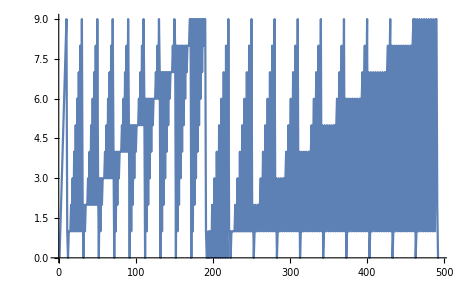
| 期望输出： |  
  | -Graphics- |

创建 4 步与分形谢尔宾斯基图样类似的 “门格海绵”，核心形式为 {{#,#,#},{#,0,#},{#,#,#}}。»


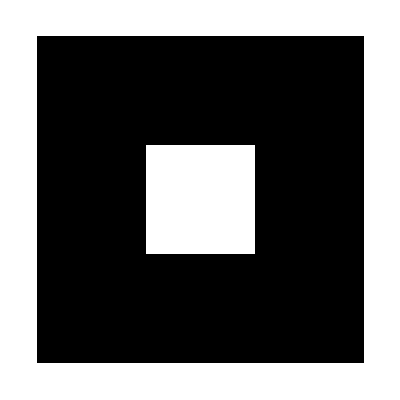
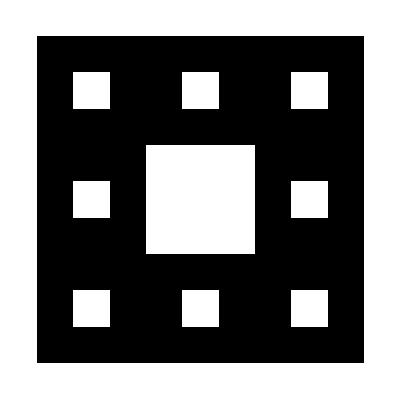
| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

通过选择 {x,y,Sqrt[x^2+y^2]}，找到只涉及整数的毕达哥拉斯三角，其中 x 和 y 最大为 20。»

| 期望输出： |  
  | {{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}} |

求 2^n 中各位数字相同的最长数列的长度，n 最大为 100。»

| 期望输出： |  
  | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,2,1,1,1,2,3,2,2,2,1,1,1,1,1,2,1,1,1,1,2,3,3,4,3,3,3,3,2,2,1,2,3,2,2,2,1,1,1,2,2,2,2,2,2,2,2,2,1,1,1,1,2,2,2,3,3,3,3,3,2,2,1,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2} |

获取 100 以内的整数名称，并根据它们的第一个字母来将它们收集到子列表中。»

| 期望输出： |  
  | {{"one","one hundred"},{"two","three","ten","twelve","thirteen","twenty","twenty-one","twenty-two","twenty-three","twenty-four","twenty-five","twenty-six","twenty-seven","twenty-eight","twenty-nine","thirty","thirty-one","thirty-two","thirty-three","thirty-four","thirty-five","thirty-six","thirty-seven","thirty-eight","thirty-nine"},{"four","five","fourteen","fifteen","forty","forty-one","forty-two","forty-three","forty-four","forty-five","forty-six","forty-seven","forty-eight","forty-nine","fifty","fifty-one","fifty-two","fifty-three","fifty-four","fifty-five","fifty-six","fifty-seven","fifty-eight","fifty-nine"},{"six","seven","sixteen","seventeen","sixty","sixty-one","sixty-two","sixty-three","sixty-four","sixty-five","sixty-six","sixty-seven","sixty-eight","sixty-nine","seventy","seventy-one","seventy-two","seventy-three","seventy-four","seventy-five","seventy-six","seventy-seven","seventy-eight","seventy-nine"},{"eight","eleven","eighteen","eighty","eighty-one","eighty-two","eighty-three","eighty-four","eighty-five","eighty-six","eighty-seven","eighty-eight","eighty-nine"},{"nine","nineteen","ninety","ninety-one","ninety-two","ninety-three","ninety-four","ninety-five","ninety-six","ninety-seven","ninety-eight","ninety-nine"}} |

将 WordList[ ] 中的前50个词按其最后一个字母排序。»

| 期望输出： |  
  | {"a","abandoned","abashed","abbreviated","abed","abalone","abase","abate","abbe","abbreviate","abdicate","abeyance","abhorrence","abidance","abide","abducting","abiding","aah","abash","aardvark","aback","abdominal","abeam","abandon","abbreviation","abdication","abdomen","abduction","aberration","abjection","abattoir","abductor","abettor","abhor","abacus","abbess","abaft","abandonment","abasement","abashment","abatement","abbot","abduct","aberrant","abet","abhorrent","abject","abbey","ability","abjectly"} |

计算前 20 个数字的平方，并按其首位数字进行排序。»

| 期望输出： |  
  | {1,16,100,121,144,169,196,25,225,256,289,36,324,361,4,49,400,64,81,9} |

按照英文名称的长度对 20 以内的整数进行排序。»

| 期望输出： |  
  | {1,2,6,10,4,5,9,3,7,8,11,12,20,15,16,13,14,18,19,17} |

从 WordList[ ] 中随机获取 20 个单词的样本，并按长度将它们收集到子列表中。»

| 期望输出示例： |  
  | {{"paste"},{"mistakenly","unintended","victorious","watercress"},{"powerful","jingoist","ballpark","rapeseed","dyslexia"},{"repeal"},{"paleontological"},{"encouragement"},{"countryside"},{"selfish","hedging"},{"barometer"},{"veil","well"},{"municipality"}} |

找出在乌克兰语(Ukrainian)中，但不在俄语(Russian)中的字母。»

| 期望输出： |  
  | {"є","і","ї","ґ"} |

使用 Intersection 来寻找同时出现在前 100 个数字的平方和立方中的数字。»

| 期望输出： |  
  | {1,64,729,4096} |

找出同时属于北约(NATO)和八国集团(G8)的国家。»

| 期望输出： |  
  | {"Canada","France","Germany","Italy","United Kingdom","United States"} |

创建一个网格，将数字 1 到 4 所有可能的排列组合作为连续的列。»

| 期望输出： |  
  | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 3 | 3 | 4 | 4 | 1 | 1 | 3 | 3 | 4 | 4 | 1 | 1 | 2 | 2 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 3
3 | 4 | 2 | 4 | 2 | 3 | 3 | 4 | 1 | 4 | 1 | 3 | 2 | 4 | 1 | 4 | 1 | 2 | 2 | 3 | 1 | 3 | 1 | 2
4 | 3 | 4 | 2 | 3 | 2 | 4 | 3 | 4 | 1 | 3 | 1 | 4 | 2 | 4 | 1 | 2 | 1 | 3 | 2 | 3 | 1 | 2 | 1 |

列出所有通过排列组合 “hello” 中的字符可以得到的不同字符串。»

| 期望输出： |  
  | {"ehllo","ehlol","eholl","elhlo","elhol","ellho","elloh","elohl","elolh","eohll","eolhl","eollh","hello","helol","heoll","hlelo","hleol","hlleo","hlloe","hloel","hlole","hoell","holel","holle","lehlo","lehol","lelho","leloh","leohl","leolh","lhelo","lheol","lhleo","lhloe","lhoel","lhole","lleho","lleoh","llheo","llhoe","lloeh","llohe","loehl","loelh","lohel","lohle","loleh","lolhe","oehll","oelhl","oellh","ohell","ohlel","ohlle","olehl","olelh","olhel","olhle","olleh","ollhe"} |

计算包含 5 个 0 和 1 的元组，然后创建数组图示。»

| 期望输出： |  
  |  |

生成一个由 5 个随机字母组成的 10 个序列的列表。»

| 期望输出示例： |  
  | {"ayasl","icnry","ahbaa","jqkpc","orlaf","rmexo","ngrfy","vwhii","wjiqn","gngvk"} |

为 Flatten[Table[{i,j,k},{i,2},{j,2},{k,2}],2] 找到一个更简单的形式。»

| 期望输出： |  
  | {{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}} |

将维基百科上关于计算机的文章中前 1000 个字符中的字母的编号创建为数组图示，每行 30 个字母。»

| 期望输出： |  
  | -Graphics- |

将 30 以内的整数根据它们对 3 的模余值收集到列表中。»

| 期望输出： |  
  | {{1,4,7,10,13,16,19,22,25,28},{2,5,8,11,14,17,20,23,26,29},{3,6,9,12,15,18,21,24,27,30}} |

根据最后一位数字，收集 2 的前 50 个幂。»

| 期望输出： |  
  | {{2,32,512,8192,131072,2097152,33554432,536870912,8589934592,137438953472,2199023255552,35184372088832,562949953421312},{4,64,1024,16384,262144,4194304,67108864,1073741824,17179869184,274877906944,4398046511104,70368744177664,1125899906842624},{8,128,2048,32768,524288,8388608,134217728,2147483648,34359738368,549755813888,8796093022208,140737488355328},{16,256,4096,65536,1048576,16777216,268435456,4294967296,68719476736,1099511627776,17592186044416,281474976710656}} |

将从 -10 到 +10 的数字按其绝对值排序的结果创建为线条图。»

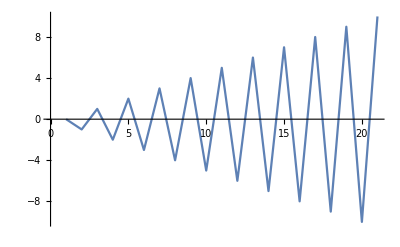
| 期望输出： |  
  | -Graphics- |

将前 200 个数字的平方按其首位数进行排序，然后绘制为线条图。»

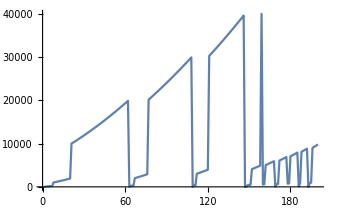
| 期望输出： |  
  | -Graphics- |

将 200 以内的整数按其英文名称的长度排序，然后绘制为线条图。»

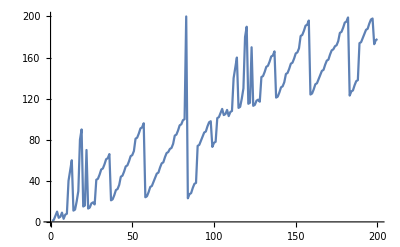
| 期望输出： |  
  | -Graphics- |

从 WordList[] 中获取 25 个随机单词样本。»

| 期望输出： |  
  | {"autopsy","reclassification","advancement","forswear","swimwear","cravat","cyclone","taps","diplomatic","effacement","peaked","ponderously","publication","immune","outstay","petrol","deaf","bilk","oddments","scoreboard","lifeless","debriefing","radiogram","doting","inter"} |

在字符串 “UNCLE” 中交互插入点号，使之变为 “U.N.C.L.E”。»

| 期望输出： |  
  | "U.N.C.L.E." |

查找出现在瑞典语(Swedish)或波兰语(Polish)中，但不在英语中的字母。»

| 期望输出： |  
  | {"ą","ę","ń","ś","ź","ż","å","ä","ć","ł","ó","ö"} |

找到加入世界卫生组织(World Health Organization)但没有加入联合国(United Nations)的国家。»

| 期望输出： |  
  | {"Cook Islands","Niue"} |

创建所有红、绿、蓝的成对混合的列表。»

| 期望输出： |  
  | {RGBColor[1, 0, 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[0, 1, 0],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[0, Rational[1, 2], Rational[1, 2]],RGBColor[0, 0, 1]} |

创建一个数组图示列表，每个包含 50 行数据，图像大小为 50，数据为连续的包含 8 个值的 0 和 1 的元组。»

| 期望输出： |  
  | {,,,,} |

生成 1000 个 4 个随机字母的序列，并列出其中出现在 WordList[ ] 中的列表。»

| 期望输出： |  
  | {"avow","frog","know","lido","snot"} |

问&答

如果块不完全吻合，Partition 会怎么做？

如果没有额外指定，它只会包括完整的块，所以它就会放弃那些只出现在不完整块中的元素。然而，如果你给定 Partition[list,UpTo[4]]，它就会创建长度最长为 4 的块，如果需要，最后一个块会更短。

技术笔记

Transpose 可以认为是对矩阵中的行和列进行转置。

ArrayFlatten 是将数组的数组压平为单一的数组，或者将一个矩阵的矩阵压平为单一的矩阵。

DeleteDuplicates[list] 的作用与 Union[list] 相同，只是它不会对元素进行重新排序。

探索更多

Wolfram 语言中的重排列与重构列表指南 »